```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
lT=100;
startT=1;
alist=Table[Flatten[Import["bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
(*alist2=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/c.dat"]],{i,1,lT}];
alist3=Table[Rest[alist2[[i]]],{i,1,lT}];*)
```

```mathematica
V1=Flatten[Transpose[Table[Flatten[Import["./dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
```

```mathematica
ρmin=0.;
ρmax=30000.;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
rhoend=500.;
```

```mathematica
(*min1=Table[Evaluate[(test=SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]](*-1.*(2ρ)^(-1/2)*),100])]==0,{i,1,lT}];*)
driv1=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]](*-1.*(2ρ)^(-1/2)*),100]/.{ρ->0}],{i,1,lT}];
```

```mathematica
(*res6=Re[Flatten[ParallelMap[FindRoot[#,{ρ,3.},WorkingPrecision->90]&,min1]][[All,2]]]*)
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/100*(i-1)]//N,{i,1,100}];
slop=Table[{SetPrecision[T[[i]]/50.85897,90],SetPrecision[FindFit[Transpose[{-Log[T/50.85897],Log[1/√driv1]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,99}];
```

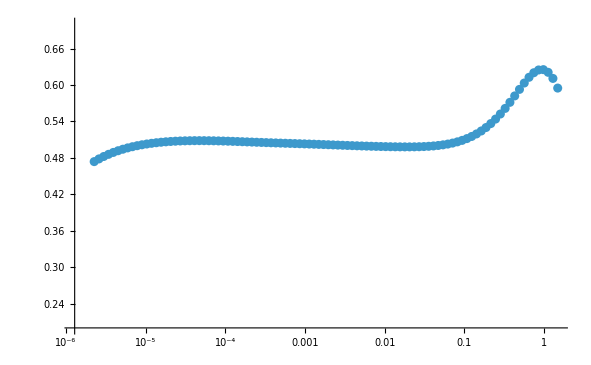

```mathematica
ListPlot[slop,ScalingFunctions->{"Log",Automatic},PlotRange->{All,{0.2,0.7}}]
```

```mathematica
Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/100*(i-1)]//N,{i,1,100}]
```

{0.0001,0.000114815,0.000131826,0.000151356,0.00017378,0.000199526,0.000229087,0.000263027,0.000301995,0.000346737,0.000398107,0.000457088,0.000524807,0.00060256,0.000691831,0.000794328,0.000912011,0.00104713,0.00120226,0.00138038,0.00158489,0.0018197,0.0020893,0.00239883,0.00275423,0.00316228,0.00363078,0.00416869,0.0047863,0.00549541,0.00630957,0.00724436,0.00831764,0.00954993,0.0109648,0.0125893,0.0144544,0.0165959,0.0190546,0.0218776,0.0251189,0.0288403,0.0331131,0.0380189,0.0436516,0.0501187,0.057544,0.0660693,0.0758578,0.0870964,0.1,0.114815,0.131826,0.151356,0.17378,0.199526,0.229087,0.263027,0.301995,0.346737,0.398107,0.457088,0.524807,0.60256,0.691831,0.794328,0.912011,1.04713,1.20226,1.38038,1.58489,1.8197,2.0893,2.39883,2.75423,3.16228,3.63078,4.16869,4.7863,5.49541,6.30957,7.24436,8.31764,9.54993,10.9648,12.5893,14.4544,16.5959,19.0546,21.8776,25.1189,28.8403,33.1131,38.0189,43.6516,50.1187,57.544,66.0693,75.8578,87.0964}